## Coursework 1

The following two subsections contain the examples from the initial coursework assignment sheet. The solved exercises are listed below.

# Example using Plot function

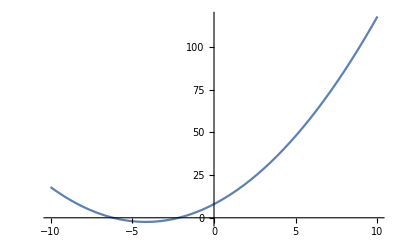

```mathematica
Plot[0.6 x^2 + 5 x + 8, {x, -10, 10}]
```

### Anti-crossing in quantum mechanics

```mathematica
symmetric2x2={{e0,v}, {v, e1}};
```

```mathematica
symmetric2x2//MatrixForm
```

(e0 | v
v | e1)

```mathematica
ham = symmetric2x2 /.{e0->x, e1->1,v->1/10};
```

```mathematica
ham // MatrixForm
```

(x | 1/10
1/10 | 1)

```mathematica
evals=Eigenvalues[ham]
```

{1/10 (5+5 x-√(26-50 x+25 x^2)),1/10 (5+5 x+√(26-50 x+25 x^2))}

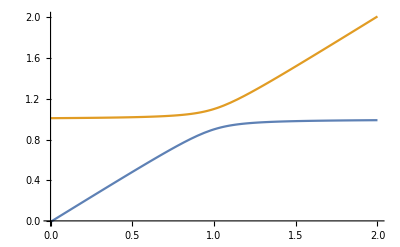

```mathematica
Plot[evals,{x,0,2}]
```

### Exercise 1: Basis state mixing

{1/10 (5+5 x-√(26-50 x+25 x^2)),1/10 (5+5 x+√(26-50 x+25 x^2))}

-Graphics-

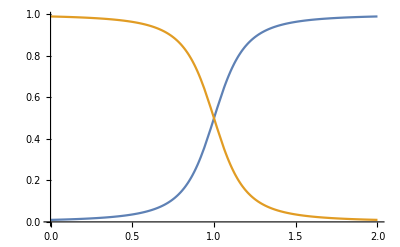

```mathematica
rules={e0->x, e1->1, v->10/100};
ham=symmetric2x2/.rules;
evals=Eigenvalues[ham]
Plot[evals,{x,0,2}]
evecs:=Eigenvectors[ham]
prob1:=Abs[Transpose[evecs][[1]]]^2;
Plot[prob1,{x,0,2}]
```

The configured Hamiltonian describes the behaviour of two energy states (e1=1 and e0=0)  that are coupled over a 
fixed interaction potential (V=1/10). The lower initial energy state is changed linearly with a parameter x.

The upper graph shows the evolution of the energies of the new eigenstates Pp and Pm as function of x, 
here now referred as E_p  and E_m. For x=0 it is E_p(0)=1=e1 and E_m(0)=0 which is the initial state without an interaction.
Until about x=0.8 E_m rises linearly with x and E_p remains roughly constant which corresponds to the behaviour of the 
initial energies without an interaction. For x>0.8 the interaction becomes relevant. The linear behavior of E_m transitions 
into constant behaviour while E_p changes from constant to linear behaviour with f(x)=x as asymptote.

The lower graph shows the probability of measuring the initial eigenstate with energy e0=0 in the resulting eigenstates
Pm (red line) and Pp(blue line). For x=0 the probability for obtaining e0 in Pm is almost 1 which means that the interaction has
only small influence on the final eigenstates. This agrees also with the energy plot where the eigenstates only differed 
from the initial energies for x>0.8. The

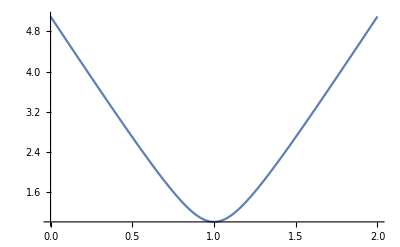

```mathematica
Plot[√(26-50 x+25 x^2), {x,0,2}]
```